```mathematica
(*Define Priors here, p1,p2,p3*)
p1:=1;
p2:=PDF[NormalDistribution[0.5,0.5],r];
p3:=DiracDelta[r-0.25];
```

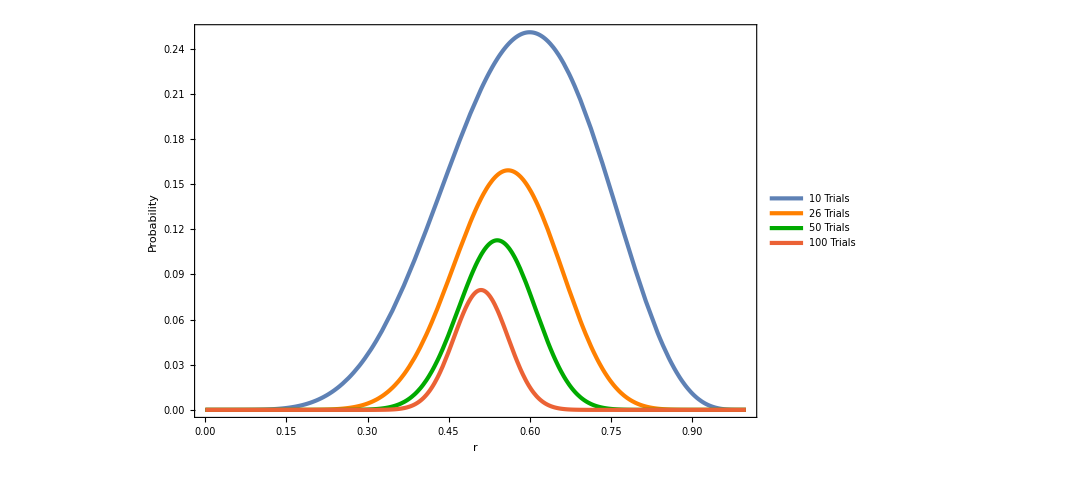

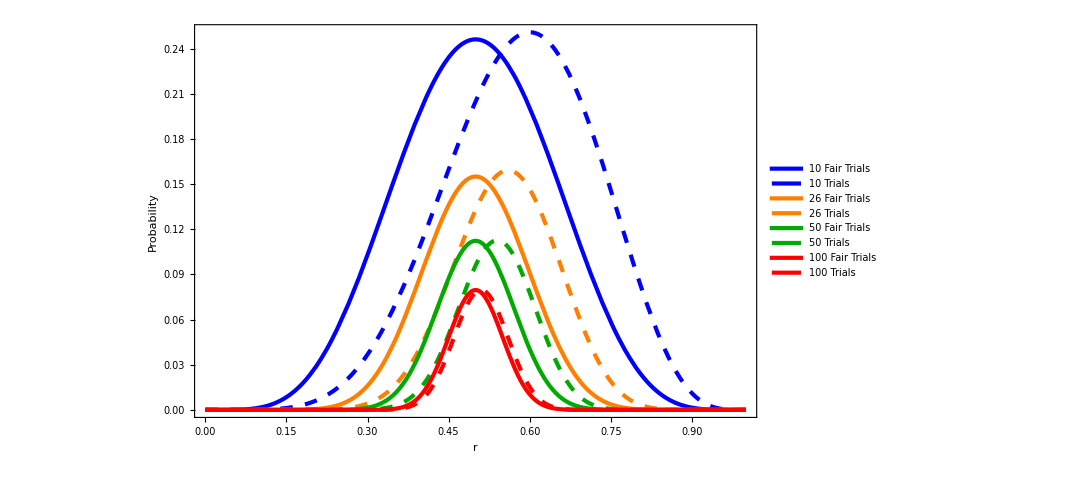

```mathematica
(*Define Binomial Distributions: p(n_H|rC)*)
(*For the Data: *)
q10[r_]:=PDF[BinomialDistribution[10,r],6];
q26[r_]:=PDF[BinomialDistribution[25,r],14];
q50[r_]:=PDF[BinomialDistribution[50,r],27];
q100[r_]:=PDF[BinomialDistribution[100,r],51];

(*For a fair coin*)
qfair10[r_]:=PDF[BinomialDistribution[10,r],5];
qfair26[r_]:=PDF[BinomialDistribution[26,r],13];
qfair50[r_]:=PDF[BinomialDistribution[50,r],25];
qfair100[r_]:=PDF[BinomialDistribution[100,r],50];

(*Plot the Binomial Distributions*)
f1=Plot[{q10[r],q26[r], q50[r],q100[r]},{r,0,1}, PlotLegends->Placed[LineLegend[{"10 Trials","26 Trials","50 Trials","100 Trials"},
LabelStyle->{Black,Bold,18},LegendLayout->{"Column",1}],{0.2,0.85}], PlotRange->All, ImageSize->800, Frame->True, FrameLabel->{r,Probability}, PlotStyle->{AbsoluteThickness[3], {Orange, AbsoluteThickness[3]},{Darker[Green], AbsoluteThickness[3]}}, BaseStyle->{FontSize->24}, Axes->False]
(*Plot all of the Binomial Distributions as a check*)
f2=Plot[{qfair10[r],q10[r],qfair26[r],q26[r],qfair50[r],q50[r],qfair100[r],q100[r]},{r,0,1}, PlotLegends->Placed[LineLegend[{"10 Fair Trials","10 Trials","26 Fair Trials","26 Trials","50 Fair Trials","50 Trials","100 Fair Trials", "100 Trials"},
LabelStyle->{Black,Bold,15},LegendLayout->{"Column",1}],{0.15,0.75}], PlotRange->All, ImageSize->800, Frame->True, FrameLabel->{r,Probability}, PlotStyle->{{Blue,AbsoluteThickness[3]},{Blue,AbsoluteThickness[3],Dashing[Medium]}, {Orange, AbsoluteThickness[3]},{Orange,AbsoluteThickness[3],Dashing[Medium]},{Darker[Green], AbsoluteThickness[3]}, {Darker[Green], AbsoluteThickness[3], Dashing[Medium]}, {Red, AbsoluteThickness[3]}, {Red, AbsoluteThickness[3], Dashing[Medium]}}, BaseStyle->{FontSize->24}, Axes->False]
Export["binom_dist.pdf",f2]
```

```mathematica
(*Define p(n_H|C) from Normalization condition*)
t10norm1:=NIntegrate[p1*q10[r],{r,0,1}];
t10norm2:=NIntegrate[p2*q10[r],{r,0,1}];
t10norm3:=Integrate[p3*q10[r],{r,0,1}];

t10fairnorm1:=NIntegrate[p1*qfair10[r],{r,0,1}];
t10fairnorm2:=NIntegrate[p2*qfair10[r],{r,0,1}];
t10fairnorm3:=Integrate[p3*qfair10[r],{r,0,1}];

t26norm1:=NIntegrate[p1*q26[r],{r,0,1}];
t26norm2:=NIntegrate[p2*q26[r],{r,0,1}];
t26norm3:=Integrate[p3*q26[r],{r,0,1}];

t26fairnorm1:=NIntegrate[p1*qfair26[r],{r,0,1}];
t26fairnorm2:=NIntegrate[p2*qfair26[r],{r,0,1}];
t26fairnorm3:=Integrate[p3*qfair26[r],{r,0,1}];

t50norm1:=NIntegrate[p1*q50[r],{r,0,1}];
t50norm2:=NIntegrate[p2*q50[r],{r,0,1}];
t50norm3:=Integrate[p3*q50[r],{r,0,1}];

t50fairnorm1:=NIntegrate[p1*qfair50[r],{r,0,1}];
t50fairnorm2:=NIntegrate[p2*qfair50[r],{r,0,1}];
t50fairnorm3:=Integrate[p3*qfair50[r],{r,0,1}];

t100norm1:=NIntegrate[p1*q100[r],{r,0,1}];
t100norm2:=NIntegrate[p2*q100[r],{r,0,1}];
t100norm3:=Integrate[p3*q100[r],{r,0,1}];

t100fairnorm1:=NIntegrate[p1*qfair100[r],{r,0,1}];
t100fairnorm2:=NIntegrate[p2*qfair100[r],{r,0,1}];
t100fairnorm3:=Integrate[p3*qfair100[r],{r,0,1}];

Grid[{{Text[p(Subscript[n,H]|C)],SpanFromLeft},{prior,1,2,3},{10trials,t10norm1,t10norm2,t10norm3},{10fair trials,t10fairnorm1,t10fairnorm2,t10fairnorm3},{26trials,t26norm1,t26norm2,t26norm3},{26fair trials,t26fairnorm1,t26fairnorm2,t26fairnorm3},{50trials,t50norm1,t50norm2,t50norm3},{50fair trials,t50norm1,t50norm2,t50norm3},{100trials,t100norm1,t100norm2,t100norm3},{100fair trials,t100fairnorm1,t100fairnorm2,t100fairnorm3}},Frame->All]
```

p (n_H|C) |  |  | 
prior | 1 | 2 | 3
10 trials | 0.0909091 | 0.0690347 | 0.016222
10 fair trials | 0.0909091 | 0.0698781 | 0.0583992
26 trials | 0.0384615 | 0.0299796 | 0.000701319
26 fair trials | 0.037037 | 0.0290538 | 0.00368192
50 trials | 0.0196078 | 0.015455 | 8.02393×10^-6
50 fair trials | 0.0196078 | 0.015455 | 8.02393×10^-6
100 trials | 0.00990099 | 0.00786029 | 1.47298×10^-8
100 fair trials | 0.00990099 | 0.00786177 | 4.50735×10^-8

```mathematica
(*Define Posterior Probabilities p(r|n_H C) *)
post10p1:=p1*q10[r]/t10norm1;
post10p2:=p2*q10[r]/t10norm2;
post10p3:=p3*q10[r]/t10norm3;

post10fairp1:=p1*qfair10[r]/t10fairnorm1;
post10fairp2:=p2*qfair10[r]/t10fairnorm2;
post10fairp3:=p3*qfair10[r]/t10fairnorm3;

post26p1:=p1*q26[r]/t26norm1;
post26p2:=p2*q26[r]/t26norm2;
post26p3:=p3*q26[r]/t26norm3;

post26fairp1:=p1*qfair26[r]/t26fairnorm1;
post26fairp2:=p2*qfair26[r]/t26fairnorm2;
post26fairp3:=p3*qfair26[r]/t26fairnorm3;

post50p1:=p1*q50[r]/t50norm1;
post50p2:=p2*q50[r]/t50norm2;
post50p3:=p3*q50[r]/t50norm3;

post50fairp1:=p1*qfair50[r]/t50fairnorm1;
post50fairp2:=p2*qfair50[r]/t50fairnorm2;
post50fairp3:=p3*qfair50[r]/t50fairnorm3;

post100p1:=p1*q100[r]/t100norm1;
post100p2:=p2*q100[r]/t100norm2;
post100p3:=p3*q100[r]/t100norm3;

post100fairp1:=p1*qfair100[r]/t100fairnorm1;
post100fairp2:=p2*qfair100[r]/t100fairnorm2;
post100fairp3:=p3*qfair100[r]/t100fairnorm3;

Grid[{{Text["Posterior Probability Distributions:" p(r|Subscript[n,H]C)],SpanFromLeft},{prior,1,2,3},{10trials,post10p1,post10p2,post10p3},{10fair trials,post10fairp1,post10fairp2,post10fairp3},{26trials,post26p1,post26p2,post26p3},{26fair trials,post26fairp1,post26fairp2,post26fairp3},{50trials,post50p1,post50p2,post50p3},{50fair trials,post50fairp1,post50fairp2,post50fairp3},{100trials,post100p1,post100p2,post100p3},{100fair trials,post100fairp1,post100fairp2,post100fairp3}},Frame->All]
```

Posterior Probability Distributions: p (r|C n_H) |  |  | 
prior | 1 | 2 | 3
10 trials | 2310. (1-r)^4 r^6 | 2427.12 ⅇ^(-2. (-0.5+r)^2) (1-r)^4 r^6 | 12945.4 (1-r)^4 r^6 DiracDelta[-0.25+r]
10 fair trials | 2772. (1-r)^5 r^5 | 2877.39 ⅇ^(-2. (-0.5+r)^2) (1-r)^5 r^5 | 4315.13 (1-r)^5 r^5 DiracDelta[-0.25+r]
26 trials | 1.15892×10^8 (1-r)^11 r^14 | 1.1863×10^8 ⅇ^(-2. (-0.5+r)^2) (1-r)^11 r^14 | 6.35574×10^9 (1-r)^11 r^14 DiracDelta[-0.25+r]
26 fair trials | 2.80816×10^8 (1-r)^13 r^13 | 2.85625×10^8 ⅇ^(-2. (-0.5+r)^2) (1-r)^13 r^13 | 2.82477×10^9 (1-r)^13 r^13 DiracDelta[-0.25+r]
50 trials | 5.51021×10^15 (1-r)^23 r^27 | 5.57786×10^15 ⅇ^(-2. (-0.5+r)^2) (1-r)^23 r^27 | 1.34651×10^19 (1-r)^23 r^27 DiracDelta[-0.25+r]
50 fair trials | 6.44694×10^15 (1-r)^25 r^25 | 6.50751×10^15 ⅇ^(-2. (-0.5+r)^2) (1-r)^25 r^25 | 1.49613×10^18 (1-r)^25 r^25 DiracDelta[-0.25+r]
100 trials | 9.99022×10^30 (1-r)^49 r^51 | 1.00405×10^31 ⅇ^(-2. (-0.5+r)^2) (1-r)^49 r^51 | 6.71518×10^36 (1-r)^49 r^51 DiracDelta[-0.25+r]
100 fair trials | 1.019×10^31 (1-r)^50 r^50 | 1.02394×10^31 ⅇ^(-2. (-0.5+r)^2) (1-r)^50 r^50 | 2.23837×10^36 (1-r)^50 r^50 DiracDelta[-0.25+r]

```mathematica
(*For visual Purposes, we define a gaussian of narrow width to demonstrate the posterior probability of p3, which is of the form of a Dirac Delta Function*)
post10p3A:=(3/400)*PDF[NormalDistribution[.25,0.001],r]
post100p3A:=8/400*PDF[NormalDistribution[0.25,0.001],r]
```

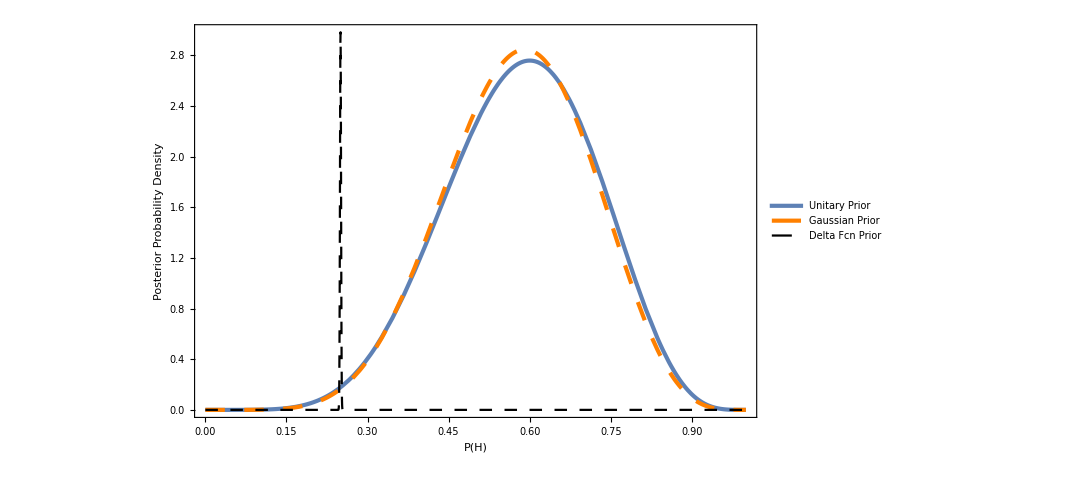

```mathematica
(*Plot the Posterior PDFs for 10 Trials, this will be used for comparison of the priors*)
{{}}
f23=Plot[{post10p1,post10p2,post10p3A},{r,0,1}, PlotLegends->Placed[LineLegend[{"Unitary Prior","Gaussian Prior","Delta Fcn Prior"},LabelStyle->{Black,Bold,18},LegendLayout->{"Column",1}],{0.85,0.85}], PlotRange->All, ImageSize->800, Frame->True, FrameLabel->{"P(H)","Posterior Probability Density"}, PlotStyle->{AbsoluteThickness[3], {Orange,Dashing[Large], AbsoluteThickness[3]},{Black,Dashing[Medium]}}, BaseStyle->{FontSize->24}, Axes->False]
Export["postPDF10Trials.pdf",f23]
```

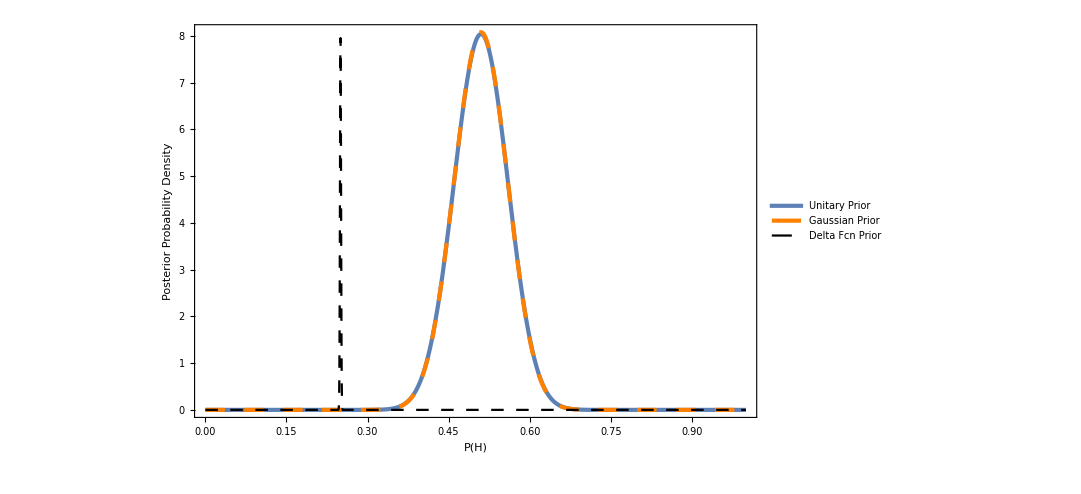

```mathematica
(*Plot the Posterior PDFs for 10 Trials, this will be used for comparison of the priors*)
f22=Plot[{post100p1,post100p2,post100p3A},{r,0,1}, PlotLegends->Placed[LineLegend[{"Unitary Prior","Gaussian Prior","Delta Fcn Prior"},LabelStyle->{Black,Bold,18},LegendLayout->{"Column",1}],{0.85,0.85}], PlotRange->All, ImageSize->800, Frame->True, FrameLabel->{"P(H)","Posterior Probability Density"}, PlotStyle->{AbsoluteThickness[3], {Orange,Dashing[Large], AbsoluteThickness[3]},{Black,Dashing[Medium]}}, BaseStyle->{FontSize->24}, Axes->False]
Export["postPDF100Trials.pdf",f22]
```

```mathematica
(*Determine Median and Interquartile Range of Each Posterior PDF *)

(*Fair Coin*)
	cdf10fair[x_]:=NIntegrate [post10fairp1,{r,0,x}]
	cdf26fair[x_]:=NIntegrate [post26fairp1,{r,0,x}]
	cdf50fair[x_]:=NIntegrate [post50fairp1,{r,0,x}]
	cdf100fair[x_]:=NIntegrate [post100fairp1,{r,0,x}]

	(*Interpolate Inverse CDFs for each of the priors in both trials*)
	invCdf10fair:=Interpolation[Table[{cdf10fair[y],y},{y,0,1,0.005}]]
	invCdf26fair:=Interpolation[Table[{cdf26fair[y],y},{y,0,1,0.005}]]
	invCdf50fair:=Interpolation[Table[{cdf50fair[y],y},{y,0,1,0.005}]]
	invCdf100fair:=Interpolation[Table[{cdf100fair[y],y},{y,0,1,0.01}]]

	(*Determine the Median*)
	M10fair:=invCdf10fair[.5]
	M26fair:=invCdf26fair[.5]
	M50fair:=invCdf50fair[.5]
	M100fair:=invCdf100fair[.5]

	(*Determine Quartile 2*)
	LQ10fair:=invCdf10fair[.25]
	LQ26fair:=invCdf26fair[.25]
	LQ50fair:=invCdf50fair[.25]
	LQ100fair:=invCdf100fair[.25]

	(*Determine Quartile 3*)
	HQ10fair:= invCdf10fair[.75]
	HQ26fair:= invCdf26fair[.75]
	HQ50fair:= invCdf50fair[.75]
	HQ100fair:= invCdf100fair[.75]
```

```mathematica
(*Data*)
	cdf10[x_]:=NIntegrate [post10p1,{r,0,x}]
	cdf26[x_]:=NIntegrate [post26p1,{r,0,x}]
	cdf50[x_]:=NIntegrate [post50p1,{r,0,x}]
	cdf100[x_]:=NIntegrate [post100p1,{r,0,x}]

	(*Interpolate Inverse CDFs for each of the priors in both trials*)
	invCdf10:=Interpolation[Table[{cdf10[y],y},{y,0,1,0.005}]]
	invCdf26:=Interpolation[Table[{cdf26[y],y},{y,0,1,0.005}]]
	invCdf50:=Interpolation[Table[{cdf50[y],y},{y,0,1,0.005}]]
	invCdf100:=Interpolation[Table[{cdf100[y],y},{y,0,1,0.012}]]

	(*Determine the Median*)
	M10:=invCdf10[.5]
	M26:=invCdf26[.5]
	M50:=invCdf50[.5]
	M100:=invCdf100[.5]

	(*Determine Quartile 1*)
	LQ10:=invCdf10[.25]
	LQ26:=invCdf26[.25]
	LQ50:=invCdf50[.25]
	LQ100:=invCdf100[.25]

	(*Determine Quartile 3*)
	HQ10:= invCdf10[.75]
	HQ26:= invCdf26[.75]
	HQ50:= invCdf50[.75]
	HQ100:= invCdf100[.75]
```

```mathematica
f4=Grid[{{Text["Quartile Determination"],SpanFromLeft},{"" ,Median,"Q1","Q3","Interquartile Range"},{"Data:10trials",M10,LQ10,HQ10,HQ10-LQ10},{"Fair Coin:10 trials",M10fair,LQ10fair,HQ10fair,HQ10fair-LQ10fair},{"Data:26trials",M26,LQ26,HQ26,HQ26-LQ26},{"Fair Coin:26trials",M26fair,LQ26fair,HQ26fair,HQ26fair-LQ26fair},{"Data:50trials",M50,LQ50,HQ50,HQ50-LQ50},{"Fair Coin:50trials",M50fair,LQ50fair,HQ50fair,HQ50fair-LQ50fair},{"Data:100trials",M100,LQ100,HQ100,HQ100-LQ100},{"Fair Coin:100trials",M100fair,LQ100fair,HQ100fair,HQ100fair-LQ100fair}},Frame->All]
Export["quartiledetermination.pdf",f4]
```

Quartile Determination |  |  |  | 
 | Median | Q1 | Q3 | Interquartile Range
Data:10trials | 0.58811 | 0.488927 | 0.682653 | 0.193726
Fair Coin:10 trials | 0.5 | 0.40158 | 0.59842 | 0.196841
Data:26trials | 0.556947 | 0.491497 | 0.621095 | 0.129598
Fair Coin:26trials | 0.5 | 0.435961 | 0.564039 | 0.128078
Data:50trials | 0.538958 | 0.491983 | 0.585475 | 0.093492
Fair Coin:50trials | 0.5 | 0.453111 | 0.546889 | 0.0937776
Data:100trials | 0.509868 | 0.476433 | 0.543245 | 0.0668125
Fair Coin:100trials | 0.5 | 0.466575 | 0.533425 | 0.066849

```mathematica
Grid[{{Text["Quartile Overlap"],SpanFromLeft},{"Trials","X_{overlap}"},{"10",HQ10fair-LQ10},{"26",HQ26fair-LQ26},{"50",HQ50fair-LQ50},{"100",HQ100fair-LQ100}},Frame->All]
```

Quartile Overlap | 
Trials | X_{overlap}
10 | 0.109493
26 | 0.0725421
50 | 0.0549057
100 | 0.0569915

```mathematica
f41=Grid[{{Text["Percentage of Overlap"],SpanFromLeft},{"Trials","X_{overlap}/R_{fair}"},{"10",(HQ10fair-LQ10)/(HQ10fair-LQ10fair)},{"26",(HQ26fair-LQ26)/(HQ26fair-LQ26fair)},{"50",(HQ50fair-LQ50)/(HQ50fair-LQ50fair)},{"100",(HQ100fair-LQ100)/(HQ100fair-LQ100fair)}},Frame->All]
Export["percentageOfOverlap.pdf",f41]
```

Percentage of Overlap | 
Trials | X_{overlap}/R_{fair}
10 | 0.556253
26 | 0.566391
50 | 0.585489
100 | 0.852541

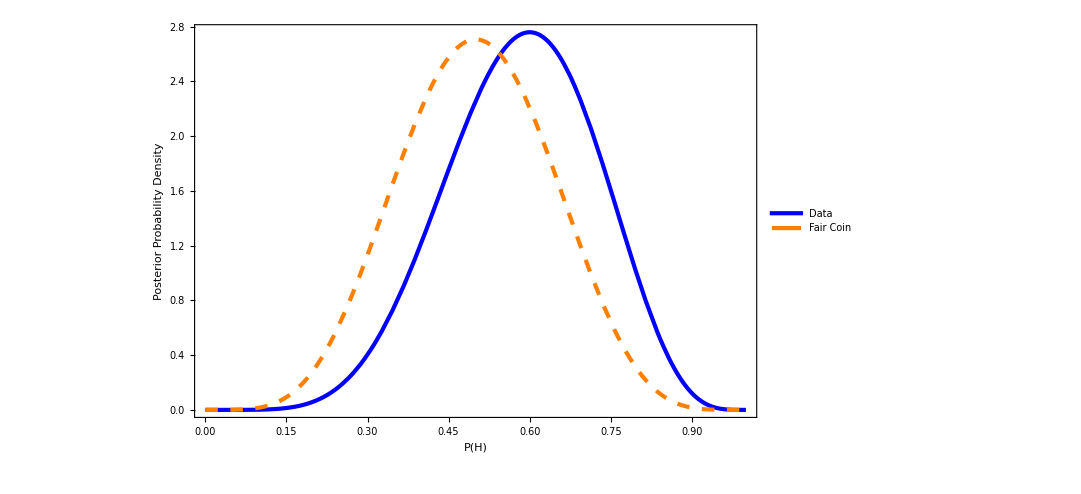

```mathematica
(*The next four plots are of the data and projected fair coin Posterior PDFs. These will be used to assess the fairness of the coin.*)


f51=Plot[{post10p1,post10fairp1},{r,0,1}, PlotLegends->Placed[LineLegend[{"Data","Fair Coin"},LabelStyle->{Black,Bold,15},LegendLayout->{"Column",1}],{0.85,0.85}], PlotRange->All, ImageSize->800, Frame->True, FrameLabel->{"P(H)","Posterior Probability Density"}, PlotStyle->{{Blue,AbsoluteThickness[3]},{Orange,AbsoluteThickness[3],Dashing[Medium]}}, BaseStyle->{FontSize->24}, Axes->False]
Export["postPDFcomparison10Trials.pdf",f51]
```

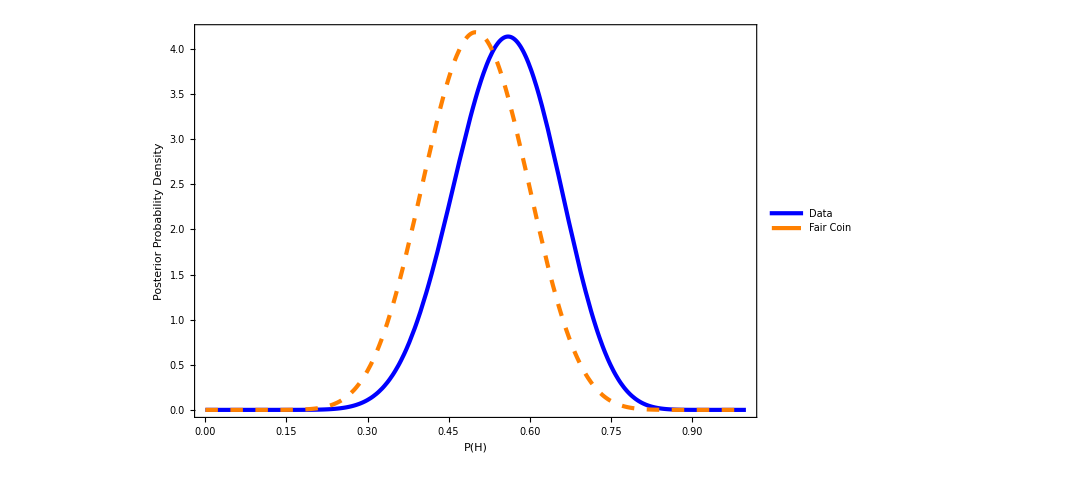

```mathematica
f52=Plot[{post26p1,post26fairp1},{r,0,1}, PlotLegends->Placed[LineLegend[{"Data","Fair Coin"},LabelStyle->{Black,Bold,15},LegendLayout->{"Column",1}],{0.85,0.85}], PlotRange->All, ImageSize->800, Frame->True, FrameLabel->{"P(H)","Posterior Probability Density"}, PlotStyle->{{Blue,AbsoluteThickness[3]},{Orange,AbsoluteThickness[3],Dashing[Medium]}}, BaseStyle->{FontSize->24}, Axes->False]
Export["postPDFcomparison26Trials.pdf",f52]
```

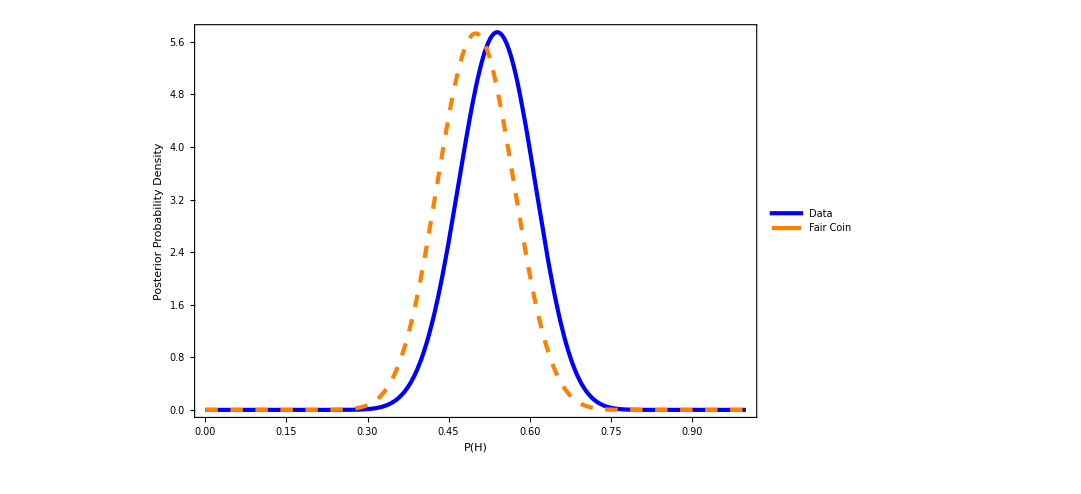

```mathematica
f53=Plot[{post50p1,post50fairp1},{r,0,1}, PlotLegends->Placed[LineLegend[{"Data","Fair Coin"},LabelStyle->{Black,Bold,15},LegendLayout->{"Column",1}],{0.85,0.85}], PlotRange->All, ImageSize->800, Frame->True, FrameLabel->{"P(H)","Posterior Probability Density"}, PlotStyle->{{Blue,AbsoluteThickness[3]},{Orange,AbsoluteThickness[3],Dashing[Medium]}}, BaseStyle->{FontSize->24}, Axes->False]
Export["postPDFcomparison50Trials.pdf",f53]
```

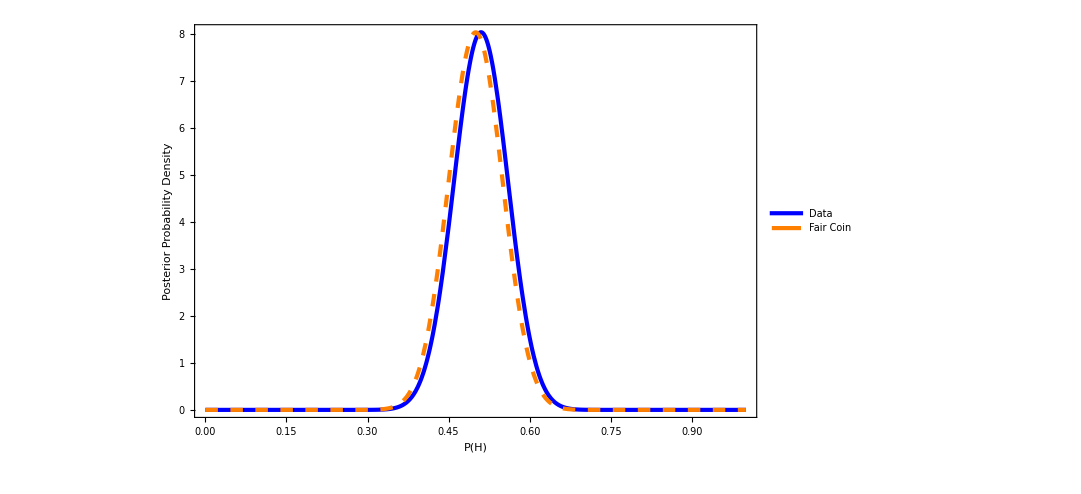

```mathematica
f54=Plot[{post100p1,post100fairp1},{r,0,1}, PlotLegends->Placed[LineLegend[{"Data","Fair Coin"},LabelStyle->{Black,Bold,15},LegendLayout->{"Column",1}],{0.85,0.85}], PlotRange->All, ImageSize->800, Frame->True, FrameLabel->{"P(H)","Posterior Probability Density"}, PlotStyle->{{Blue,AbsoluteThickness[3]},{Orange,AbsoluteThickness[3],Dashing[Medium]}}, BaseStyle->{FontSize->24}, Axes->False]
Export["postPDFcomparison100Trials.pdf",f54]
```

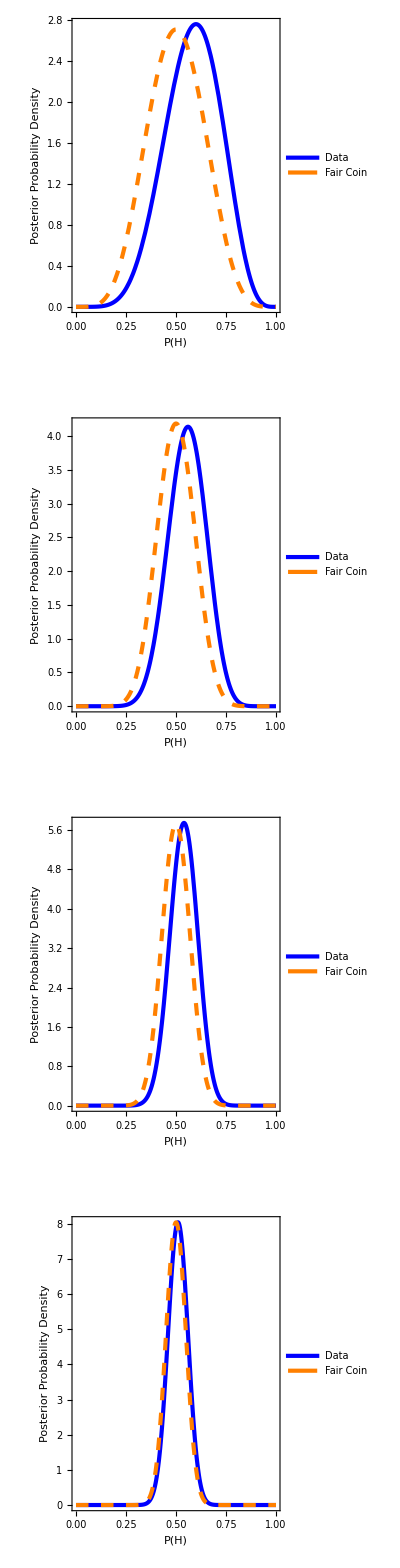

```mathematica
f7=GraphicsGrid[{{f51},{f52},{f53},{f54}},ImageSize->Full]
Export["postProbGrid.pdf",f7]
```